```mathematica
(* Parámetros *)
cu=0.5;
mmx=6;

(* Calculo *)
SetSharedVariable[prog];
prog = 0;
FRII[x_,y_]:=If[(x-1.)^2.+(y-1.)^2.<1&&x<1.+cu,0,1];
ϕm[x_,y_,m1_,m2_]:= Sin[(π m1 x)/2]Sin[(π m2 y)/2];
Bas=Flatten[Table[{m1,m2},{m1,1,mmx},{m2,1,mmx}],1];
Monitor[HND=ParallelTable[prog++;
Quiet[
NIntegrate[ϕm[x,y,Bas[[k1,1]],Bas[[k1,2]]]FRII[x,y] ϕm[x,y,Bas[[k2,1]],Bas[[k2,2]]],{x,0,2},{y,0,2},AccuracyGoal->8,
Method->"MultidimensionalRule"
]
],
{k1,1,Length[Bas]},{k2,1,Length[Bas]}];,{prog,mmx^4}
]
HD=DiagonalMatrix[Table[0.5 Pi^2(Bas[[k,1]]^2+Bas[[k,2]]^2)/4,{k,1,Length[Bas]}]];
HM=HD+200000.HND;
NEV=Eigenvalues[HM];
EV=Sort[NEV];
Evec=Eigenvectors[HM][[Ordering[NEV]]];

(* Gráficas *)
SetOptions[{DensityPlot},BaseStyle->{FontSize->14}];
phisolution[x_,y_,nes_]:=Sum[Evec[[nes,k]] ϕm[x,y,Bas[[k,1]],Bas[[k,2]]],{k,1,Length[Bas]}];
Manipulate[
DensityPlot[phisolution[x,y,nes]^2,{x,0,2},{y,0,2},RegionFunction->Function[{x,y,z},Sqrt[(x-1)^2+(y-1)^2]<1&&x<1+cu],
Axes->True,
AxesLabel->{"x", "y"},
AxesOrigin->{1,1},
ColorFunction->"Rainbow",
PlotLegends->Placed[
BarLegend[Automatic,LegendMarkerSize->Automatic,LabelStyle->{FontSize->13},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendLabel->"\!\(\*SuperscriptBox[\(ψ\), \(2\)]\)"
],{After,Top}
],
Mesh->Automatic,
ImageSize->300
],
{nes,1,Length[Evec],1},
ContinuousAction->False,
SynchronousUpdating->False,
ControllerLinking->False
]
```

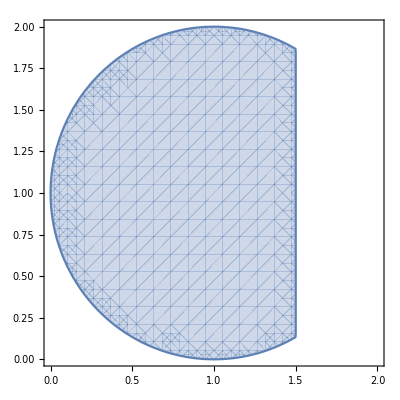

```mathematica
(* Visualizar region *)
RegionPlot[(x-1)^2+(y-1)^2<1&&x<1+cu,{x,0,2},{y,0,2}]
```

```mathematica
EV
```

{5.92915,11.576,16.9423,22.0206,27.4379,33.9952,131.523,259.538,282.45,353.654,489.162,642.525,878.537,982.668,1163.41,2081.9,2332.17,2895.56,19759.,26433.8,31309.6,39328.8,74685.6,74826.,76299.9,79050.2,80602.9,85753.3,147276.,162153.,196956.,196972.,197032.,197098.,197500.,197666.}